# Esercizio B

```mathematica
Clear["Global`*"]
```

Si vuole studiare il comportamento del sistema proprio LTI-TC {
 dove

```mathematica
A={{1, -1, 0}, {76/125, -139/125, -64/125}, {-201/125, 139/125, -61/125}}
B={{0}, {-1}, {1}}
C1={{1, 0, 0}}
```

{{1,-1,0},{76/125,-139/125,-64/125},{-201/125,139/125,-61/125}}

{{0},{-1},{1}}

{{1,0,0}}

```mathematica
A // MatrixForm
B // MatrixForm
C1 // MatrixForm
```

(1 | -1 | 0
76/125 | -139/125 | -64/125
-201/125 | 139/125 | -61/125)

(0
-1
1)

(1 | 0 | 0)

Il sistema assegnato è proprio in quanto la matrice ingresso-uscita , è pari a .

## 1. Modi naturali

I modi naturali caratterizzano qualitativamente il comportamento di un sistema dinamico in evoluzione libera. Essi sono legati agli autovalori della matrice  e sono essenziali per studiare il comportamento della risposta forzata.

Calcolo gli autovalori di A che coincidono con le soluzioni del suo polinomio caratteristico

```mathematica
λ=Eigenvalues[A]
```

{-1/5,-1/5,-1/5}

Essendo tutti gli autovalori strettamente inferiori di uno, i modi naturali del sistema convergeranno a zero.

```mathematica
CP=CharacteristicPolynomial[A,x]
```

-1/125-(3 x)/25-(3 x^2)/5-x^3

```mathematica
Solve[CP==0]
```

{{x→-1/5},{x→-1/5},{x→-1/5}}

Gli autovalori o meglio, l’autovalore è reale e multiplo cioè ha molteplicità algebrica pari a tre. Avendo tutti parte modulo <=1, il sistema è asintoticamente stabile. Devo verificare che la matrice A sia diagonalizzabile, condizione necessaria è che la molteplicità algebrica di un autovalore sia pari alla sua molteplicità geometrica, questo per ogni autovalore nello spettro di A. Calcolo dunque la molteplicità geometrica, ovvero la dimensione della base di Ker(A-λI)

```mathematica
NullSpace[A-λ[[1]] IdentityMatrix[3]]
```

{{-20/19,-24/19,1}}

La molteplicità geometrica è pari a uno, dunque la matrice A non è diagonalizzabile. Per procedere si farà uso della forma canonica di Jordan, generalizzazione della forma canonica digitale. La matrice A  è simile, tramite una oppurtuna matrice T, matrice di cambiamento di base non singolare ad una forma diagonale a blocchi.

Costruisco la matrice di cambiamento di base T e la matrice di Jordan Λ

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{-20/19,225/361,-17375/6859},{-24/19,650/361,-25125/6859},{1,0,0}},{{-1/5,1,0},{0,-1/5,1},{0,0,-1/5}}}

```mathematica
T//MatrixForm
```

(-20/19 | 225/361 | -17375/6859
-24/19 | 650/361 | -25125/6859
1 | 0 | 0)

```mathematica
Λ//MatrixForm
```

(-1/5 | 1 | 0
0 | -1/5 | 1
0 | 0 | -1/5)

Si ha un unico blocco associato all’autovalore . I modi naturali del sistema a tempo discreto, sono del tipo polinomial-potenza e vengono indivituati facilmente con la matrice :

```mathematica
=MatrixPower[Λ,k] //MatrixForm
```

((-1/5)^k | -(-1)^k 5^(1-k) k | 1/2 (-1)^k 5^(2-k) (-1+k) k
0 | (-1/5)^k | -(-1)^k 5^(1-k) k
0 | 0 | (-1/5)^k)

I modi naturali sono tre e sono: , (k
1) , (k
2) .La verifica del numero di modi naturali si può fare attraverso il grado del polinomio minimo

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

1/125 (1+5 x)^3

Come volevasi verificare.

Grafico dei modi naturali

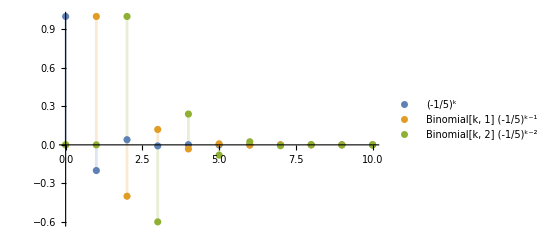

```mathematica
DiscretePlot[{(-1/5)^k,Binomial[k,1](-1/5)^(k-1),Binomial[k,2](-1/5)^(k-2)},{k,0,10},PlotRange->All, PlotLegends->"Expressions"]
```

Anche il grafico mostra come i modi naturali di natura pseudo-oscillatoria, convergano a zero.

## 2. Risposta libera

La risposta libera nello stato per un sistema LTI-TD è pari a: , mentre la risposta libera nell’uscita, è pari a: Posso perciò calcolare la risposta libera nello stato anche utilizzando , cioè lo stato iniziale  proiettato lungo le colonne di , matrice di cambiamento di base, e la matrice di Jordan .

```mathematica
={{-1}, {-2}, {3}}
```

{{-1},{-2},{3}}

```mathematica
=Inverse[T].
```

{{3},{-37/25},{-152/125}}

```mathematica
[k_]:=Simplify[T.MatrixPower[Λ,k].]
```

```mathematica
[k] //MatrixForm
```

((-1/5)^k (-1-20 k+16 k^2)
2 (-1)^k 5^(-1-k) (-5-44 k+48 k^2)
(-1/5)^(1+k) (-15-113 k+76 k^2))

La risposta libera è ottenuta come combinazione lineare dei modi del sistema, anche se attraverso Mathematica non si intuisce, sono presenti tutti i modi naturali. Verifico il risultato calcolando la risposta libera nello stato attraverso la sua definizione

```mathematica
[k_]:=Simplify[MatrixPower[A,k].]
```

```mathematica
[k] //MatrixForm
```

((-1/5)^k (-1-20 k+16 k^2)
2 (-1)^k 5^(-1-k) (-5-44 k+48 k^2)
(-1/5)^(1+k) (-15-113 k+76 k^2))

La risposta libera nell’uscita invece è pari a:

```mathematica
[k_]:=Simplify[C1.[k]]
```

```mathematica
[k]//MatrixForm
```

((-1/5)^k (-1-20 k+16 k^2))

Grafico della risposta libera nello stato

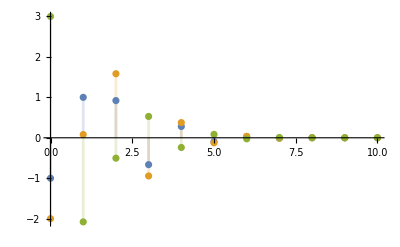

```mathematica
DiscretePlot[{[k][[1]],[k][[2]],[k][[3]]},{k,0,10},PlotRange->All]
```

Anche in questo caso dal grafico si nota che la risposta nello stato converga a zero.

## 3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

La risposta libera nello stato è una combinazione lineare dipendente dai modi naturali del sistema, perciò scegliendo un particolare stato iniziale che è “allineato” lungo la direzione di un autovalore, sulla risposta libera si accenderanno solo i modi associati a quell’autovalore. Se invece scegliessi combinazioni lineari dei modi naturali, si attiverebbero solo i modi presenti in quella combinazione lineare. Operativamente, si pone come stato iniziale una combinazione lineare delle colonne della matrice T relative allo stato che voglio visualizzare. Avendo un solo autovalore multiplo , attivo tutte le colonne

```mathematica
=15T[[All,1]]+3T[[All,2]]+4T[[All,3]]
```

{-164975/6859,-193410/6859,15}

```mathematica
[k_]:=Simplify[MatrixPower[A,k].]
```

```mathematica
[k]//MatrixForm
```

(-((-1)^k 5^(2-k) (6599-15352 k+14440 k^2))/6859
-(2 (-1)^k 5^(1-k) (19341-31616 k+43320 k^2))/6859
(-1)^k 5^(1-k) (3-13 k+10 k^2))

Verifico proiettando lo stato lungo le colonne di

```mathematica
=Inverse[T].
```

{15,3,4}

```mathematica
[k_]:=Simplify[T.MatrixPower[Λ,k].]
```

```mathematica
[k]//MatrixForm
```

(-((-1)^k 5^(2-k) (6599-15352 k+14440 k^2))/6859
-(2 (-1)^k 5^(1-k) (19341-31616 k+43320 k^2))/6859
(-1)^k 5^(1-k) (3-13 k+10 k^2))

Come volevasi verificare.

## 4. Funzione di trasferimento, i suoi poli e zeri

La funzione di trasferimento di un sistema LTI-TD è quella funzione di variabile complessa  tale che moltiplicata algebricamente per la Z-Trasformata dell’ingresso restituisce la Z-Trasformata della risposta forzata. È definita come , ovvero il rapporto tra Z-Trasformata della risposta forzata e Z-Trasformata dell’ingresso. Esplicitando la Z-Trasformata della risposta forzata come  la funzione di trasferimento è pari . Nel caso di sistema proprio: .

```mathematica
G[z_]:=Simplify[C1.Inverse[z IdentityMatrix[3]-A].B]
```

```mathematica
G[z]
```

{{(125 (1+z))/(1+5 z)^3}}

Un polo è un numero complesso ρ tale che: , inoltre i poli sono le radici del denominatore della funzione di trasferimento ed anche un sottoinsieme dello spettro di A.
Uno zero è un numero complesso ζ  tale che: , dunque gli zeri rappresentano le radici del numeratore della funzione di trasferimento.

```mathematica
PoliFdt=Solve[Denominator[G[z]]==0,z]
```

{{z→-1/5},{z→-1/5},{z→-1/5}}

In questo caso i poli coincidono con gli autovalori di A

```mathematica
ZeriFdt=Solve[Numerator[G[z]]==0,z]
```

{{z→-1}}

Verifico i calcoli tramite funzioni built-in di Mathematica

```mathematica
Σ=StateSpaceModel[{A,B,C1}]
```

1-10076/125-139/125-64/125-1-201/125139/125-61/12511000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Simplify[TransferFunctionModel[Σ]]
```

(125 (1+s))/(1+5 s)^3TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1112511FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Σ][[1,1]]
```

{-1/5,-1/5,-1/5}

```mathematica
TransferFunctionZeros[Σ]
```

{{{-1}}}

Come volevasi verificare i risultati sono corretti.

## 5. Risposta al gradino unitario

### 5.1 Calcolo risposta al gradino unitario

Il gradino unitario è un segnale di tipo polinomiale, right-sided definito tramite notazione piecewise: Piecewise[{{1, k}, {0, k< 0}}]. Per determinare la risposta al gradino unitario, si utilizzerà la risposta forzata, che è pari al prodotto tra funzione di trasferimento e la Z-Trasformata dell’ingresso. In questo caso l’ingresso è il gradino unitario quindi si utilizzerà la Z-Trasformata del gradino unitario pari a si ricava da:  :=  considerando  := ,

```mathematica
U[z]=ZTransform[UnitStep[k],k,z]
```

z/(-1+z)

```mathematica
[z_]:=G[z]U[z]
```

```mathematica
[z]
```

{{(125 z (1+z))/((-1+z) (1+5 z)^3)}}

La risposta forzata ottenuta è però nel dominio della variabile complessa  e non nel dominio del tempo. Per ottenere la risposta forzata nel dominio del tempo, occorre antitrasformare il risultato ottenuto. Dato che la risposta forzata è esprimibile come combinazione lineare del contributo dell’ingresso più la combinazione lineare dei modi naturali. Si può utilizzare la scomposizione in fratti semplici e la formula di Heaviside per passare al dominio del tempo, ma prima di fare ciò occore dividere la risposta forzata per .

```mathematica
[z]/z
```

{{(125 (1+z))/((-1+z) (1+5 z)^3)}}

Uso heaviside

```mathematica
/(z-1)+/(z+1/5)+/(z+1/5)^2+/(z+1/5)^3
```

C_1/(-1+z)+C_21/(1/5+z)+C_22/(1/5+z)^2+C_23/(1/5+z)^3

```mathematica
=Limit[(z-1)[z]/z, z ->1]
```

{{125/108}}

```mathematica
=Limit[(z+1/5)^3[z]/z, z ->-1/5]
```

{{-2/3}}

```mathematica
=Limit[D[(z+1/5)^3[z]/z,z], z ->-1/5]
```

{{-25/18}}

```mathematica
=(1/5)Limit[D[D[(z+1/5)^3[z]/z,z],z], z ->-1/5]
```

{{-25/54}}

Moltiplico per  i fratti semplici per “sistemare”

```mathematica
(z/(z-1))+(z/(z+1/5))+(z/(z+1/5)^2)+(z/(z+1/5)^3)
```

{{(125 z)/(108 (-1+z))-(2 z)/(3 (1/5+z)^3)-(25 z)/(18 (1/5+z)^2)-(25 z)/(54 (1/5+z))}}

Dalla Z-Trasformata :=   mi ricavo la risposta forzata:

```mathematica
[k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 21](-1/5)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/5)^(k-1)UnitStep[k]+Subscript[C, 23] Binomial[k,2](-1/5)^(k-2)UnitStep[k]
```

```mathematica
[k]
```

{{(125 UnitStep[k])/108-1/54 (-1)^k 5^(2-k) UnitStep[k]-1/18 (-1)^(-1+k) 5^(3-k) k UnitStep[k]-1/3 (-1/5)^(-2+k) (-1+k) k UnitStep[k]}}

Verifico i calcoli tramite la Z-Trasformata inversa di Mathematica

```mathematica
[k_]:=Expand[InverseZTransform[[z],z,k]]
```

```mathematica
[k]
```

{{125/108-1/108 (-1)^k 5^(3-k)+11/18 (-1)^k 5^(2-k) k-1/3 (-1)^k 5^(2-k) k^2}}

Come volevasi verificare a meno di qualche manipolazione algebrica le risposte risultano uguali.

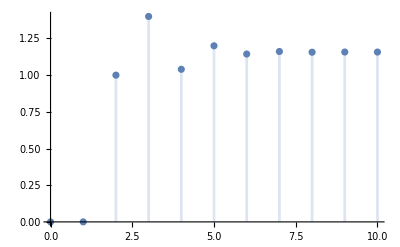

```mathematica
DiscretePlot[{[k][[1,1]]},{k,0,10},PlotRange->All]
```

La differenza tra numero di poli e numero di zeri, restituisce il numero di passi iniziali in cui la risposta al gradino è pari a zero, avendo tre poli ed uno zero il numero di passi iniziali è pari a due come il grafico della risposta mostra.

### 5.2 Scomposizione risposta

La risposta forzata è composta da: risposta a regime o steady state response, che descrive il valore a cui la risposta forzata convergere e risposta transitoria, presente solo se i modi naturali convergono. La risposta a regime è pari

```mathematica
RispRegime=UnitStep[k]
```

{{(125 UnitStep[k])/108}}

La risposta transitoria è ricavibile facilmente rimuovendo la componente a regime dalla risposta forzata ottenuta

```mathematica
RispTransitoria=[k]-RispRegime
```

{{-1/54 (-1)^k 5^(2-k) UnitStep[k]-1/18 (-1)^(-1+k) 5^(3-k) k UnitStep[k]-1/3 (-1/5)^(-2+k) (-1+k) k UnitStep[k]}}

La risposta transitoria è tale perché si esaurisce nel tempo per . Infatti si può verificare che il limite per  , della risposta transitoria è pari a zero

```mathematica
Limit[RispTransitoria,k->∞]
```

{{0}}

Grafico dellla risposta forzata evidenziando la risposta a regime e la risposta transitoria.

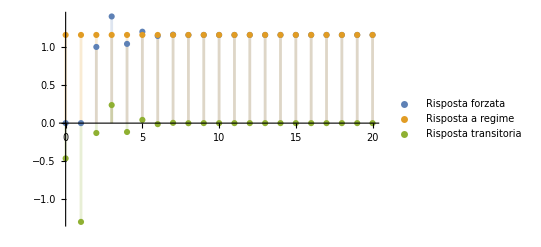

```mathematica
DiscretePlot[{[k][[1,1]],RispRegime[[1,1]],RispTransitoria[[1,1]]},{k,0,20},PlotRange->All, PlotLegends->{"Risposta forzata", "Risposta a regime", "Risposta transitoria"}]
```

## 6. Modelli ARMA e risposta all’ingresso u(k)

### 6.1 Modelli ARMA

Occorre adesso determinare i modello ARMA equivalenti, individuando le condizioni iniziali sull’uscita compatibili con lo stato iniziale .

```mathematica
xar= {{3},{3},{-3}}
```

{{3},{3},{-3}}

Per determinare il modello ARMA, occorre valutare il sistema dinamico nella rappresentazione Ingresso-Uscita. Rispetto alla rappresentazione Ingresso-Stato-Uscita, per  equivalente, qualsiasi sia l’ingresso, con condizioni iniziali nulle, l’uscita forzata corrispondente è la stessa a parità di ingresso. Ciò vale anche per la risposta libera e risposta forzata a patto che ci siano le stesse condizioni iniziali. Per prima cosa si valuta la funzione di trasferimento come un’identità dunque: (125 (1+z))/(1+5 z)^3=(Y(z))/(U(z))  da cui attraverso operazioni algebriche si ottiene la seguente equazione:

```mathematica
id=Expand[Denominator[G[z]]Yar[z]]==Expand[Numerator[G[z]]Uar[z]]
```

{{Yar[z]+15 z Yar[z]+75 z^2 Yar[z]+125 z^3 Yar[z]}}=={{125 Uar[z]+125 z Uar[z]}}

Per poter portare l’equazione dal dominio della variabile complessa  al dominio del tempo , utilizzo l’estensione ad  del teorema dell’anticipo elementare che risulta essere il seguente:  e . Dunque l’equazione diventa

```mathematica
eq=id/.  { Yar[z]-> Yar[k], z Yar[z]-> Yar[k+1], z^2 Yar[z]-> Yar[k+2], z^3  Yar[z]-> Yar[k+3],Uar[z]-> Uar[k], z Uar[z]-> Uar[k+1]}
```

{{Yar[k]+15 Yar[1+k]+75 Yar[2+k]+125 Yar[3+k]}}=={{125 Uar[k]+125 Uar[1+k]}}

L’equazione costruita, presenta solo l’ingresso e l’uscita e ho dunque la rappresentazione Ingresso-Uscita del sistema. Un altro modo per vedere il modello ARMA, è quello di trasformare gli anticipi in ritardi:

```mathematica
eq2= eq /. { Yar[k]-> Yar[k'-3], Yar[k+1]-> Yar[k'-2], Yar[k+2]-> Yar[k'-1], Yar[k+3]-> Yar[k'],Uar[k]-> Uar[k'-3], Uar[k+1]-> Uar[k'-2]}
```

{{Yar[-3+k']+15 Yar[-2+k']+75 Yar[-1+k']+125 Yar[k']}}=={{125 Uar[-3+k']+125 Uar[-2+k']}}

A questo punto risolvo l’equazione nel dominio della variabile complessa

```mathematica
eqz=ZTransform[eq,k,z] /. {ZTransform[Yar[k],k,z]-> Yar[z], ZTransform[Uar[k],k,z]-> Uar[z]}
```

{{Yar[z]+15 (-z Yar[0]+z Yar[z])+75 (-z^2 Yar[0]-z Yar[1]+z^2 Yar[z])+125 (-z^3 Yar[0]-z^2 Yar[1]-z Yar[2]+z^3 Yar[z])}}=={{125 Uar[z]+125 (-z Uar[0]+z Uar[z])}}

```mathematica
Risposta= Collect[Solve[eqz,Yar[z]][[1,1]][[2]],Uar[z]]
```

(5 (25+25 z) Uar[z])/(1+5 z)^3+(5 (-25 z Uar[0]+3 z Yar[0]+15 z^2 Yar[0]+25 z^3 Yar[0]+15 z Yar[1]+25 z^2 Yar[1]+25 z Yar[2]))/(1+5 z)^3

```mathematica
Libera= Collect[Solve[eqz,Yar[z]][[1,1]][[2]],Uar[z]][[2]]
```

(5 (-25 z Uar[0]+3 z Yar[0]+15 z^2 Yar[0]+25 z^3 Yar[0]+15 z Yar[1]+25 z^2 Yar[1]+25 z Yar[2]))/(1+5 z)^3

Per calcolare la risposta libera occorre risolvere l’equazione imponendo le condizioni iniziali sull’uscita compatibili

```mathematica
Yar[0]=C1.xar
```

{{3}}

```mathematica
Yar[1]=C1.A.xar
```

{{0}}

```mathematica
Yar[2]=C1.A.A.xar
```

{{-3/125}}

```mathematica
Uar[0]=0
```

0

```mathematica
YLiberaz[z_]:=Libera
```

```mathematica
YLiberaz[z]
```

{{(5 ((42 z)/5+45 z^2+75 z^3))/(1+5 z)^3}}

Nel dominio del tempo  è pari invece a:

```mathematica
YLibera[k_]:=Expand[InverseZTransform[YLiberaz[z],z,k]]
```

```mathematica
YLibera[k]
```

{{3 (-1/5)^k-21 (-1)^k 5^(-1-k) k+6 (-1)^k 5^(-1-k) k^2}}

### 6.2 Risposta all’ingresso

Valuto ora la risposta all’ingresso Piecewise[{{1, }, {0, k>10}, {0, k<0}}]. Per capire meglio la natura del segnale ne faccio il grafico

```mathematica
u[k_]:=Piecewise[{{1, }, {0, k>10}, {0, k<0}}]
```

```mathematica
u[k]
```

Piecewise[{{1, 0≤k≤10}, {0, True}}]

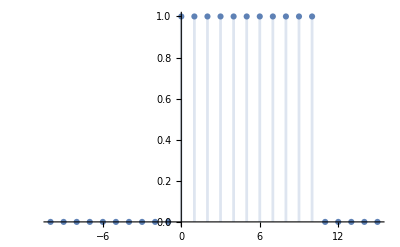

```mathematica
DiscretePlot[u[k],{k,-10,15}, PlotRange->All]
```

Si tratta dunque di un gradino unitario limitato nell’intervallo . Per calcolare la risposta al segnale, è necessario prima di tutto calcolare l’antitrasformata zeta della funzione di trasferimento

```mathematica
FdT[z_]:=Simplify[C1.Inverse[z IdentityMatrix[3]-A].B]
```

```mathematica
FdT[z]
```

{{(125 (1+z))/(1+5 z)^3}}

```mathematica
g[k_]:=InverseZTransform[FdT[z],z,k]
```

```mathematica
g[k]
```

{{(-1)^(1+k) 5^(2-k) (5-7 k+2 k^2) (1-UnitStep[-k])}}

Questa risulta essere inoltre, la risposta all’impulso, che per definizione è l’antitrasformata zeta della funzione di trasferimento del sistema. Per calcolare la risposta forzata al segnale , utilizzo la somma di convoluzione:

```mathematica
[k_]:=∑_(i=0)^k g[i]u[k-i]
```

```mathematica
[k]
```

{{Piecewise[{{-(-1)^k 5^(2-k) (2299895110-387912327 k+16276042 k^2), k>10}, {1/108 5^(2-k) (-5 (-1)^k+5^(1+k)+66 (-1)^k k-36 (-1)^k k^2), 0<k≤10}, {0, True}}]}}

Grafico della risposta

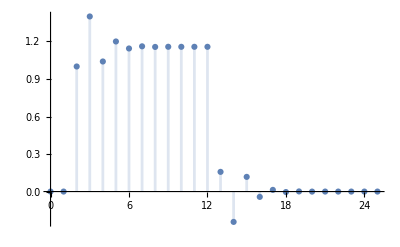

```mathematica
DiscretePlot[{[k][[1,1]]},{k,-10,25},PlotRange->All]
```

## 7. Condizioni iniziali tali che la risposta al gradino coincide con il suo valore di regime

Valgono le stesse considerazioni del sistema a tempo continuo.
Affinché la risposta al gradino coincida con il suo valore di regime, è necessario che la risposta libera vada a compensare la risposta transitoria. Per individuare tale combinazione lineare, parto definendo il vettore stato iniziale

```mathematica
x0={{x1},{x2},{x3}}
```

{{x1},{x2},{x3}}

Vado perciò a considerare come ingresso il gradino unitario discreto, la cui Z-Trasformata è la seguente:

```mathematica
[z]=z/(z-1)
```

z/(-1+z)

Calcolo la componente a regime della risposta al gradino

```mathematica
regime=(G[1][z])[[1]][[1]]
```

(125 z)/(108 (-1+z))

Calcolo la risposta libera, la risposta forzata e la risposta transitoria

```mathematica
libera=Simplify[z C1.Inverse[z IdentityMatrix[3]-A].x0][[1]][[1]]
```

(z (64 x3-x2 (61+125 z)+x1 (139+200 z+125 z^2)))/(1+5 z)^3

```mathematica
forzata=Simplify[G[z][z]][[1]][[1]]
```

(125 z (1+z))/((-1+z) (1+5 z)^3)

```mathematica
transitoria=Factor[forzata-regime]
```

-(125 z (107+200 z+125 z^2))/(108 (1+5 z)^3)

Sommo libera e transitoria, ne estraggo il numeratore e lo pongo pari a zero

```mathematica
Numerator[Simplify[Expand[libera+transitoria]]]
```

z (-13375+6912 x3-25000 z-15625 z^2-108 x2 (61+125 z)+108 x1 (139+200 z+125 z^2))

Ho tre incognite. Estraggo i coefficienti del polinomio al numeratore

```mathematica
CL=CoefficientList[Numerator[Simplify[Expand[libera+transitoria]]],z]
```

{0,-13375+15012 x1-6588 x2+6912 x3,-25000+21600 x1-13500 x2,-15625+13500 x1}

Determino le incognite  che annullano il set dei coefficienti del polinomio al numeratore

```mathematica
Solve[CL=={0,0,0,0},{x1,x2,x3}]
```

{{x1→125/108,x2→0,x3→-125/216}}

Verifico il risultato ottenuto, calcolando la risposta a partire dallo stato iniziale ricavato

```mathematica
Σ1=StateSpaceModel[{A,B,C1},SamplingPeriod->1]
```

1-10076/125-139/125-64/125-1-201/125139/125-61/125110001StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
FullSimplify[OutputResponse[{Σ1,{125/108,0,-125/216}},1,k]]
```

{125/108}

Come volevasi verificare coincide con la risposta a regime